## Set the Directory and importing files

```mathematica
aa=StringJoin[NotebookDirectory[],"hdf-data"];
SetDirectory[aa];
f=FileNames["*.HDF"];
len=Length[f];
```

```mathematica
files=Table[Import[f⟦i⟧],{i,1,len}]; (*importando o arquivo do CALIPSO - Level 1*)
```

Setting up latitude and longitude

```mathematica
fdat=FileNames["*.dat"]
```

{2012_09_12_15UTC_120h_backward_trajplot.dat,2012_09_12_17UTC_120h_backward_trajplot.dat}

```mathematica
fdatbacktraj=2;
```

```mathematica
filedat=Flatten[Table[Import[fdat⟦fdatbacktraj⟧],{i,1,1}],1];
```

```mathematica
longsp=Table[{filedat⟦i⟧⟦3⟧,filedat⟦i⟧⟦4⟧,filedat⟦i⟧⟦5⟧,filedat⟦i⟧⟦11⟧},{i,1,Length[filedat]}];
latsp=Table[{filedat⟦i⟧⟦3⟧,filedat⟦i⟧⟦4⟧,filedat⟦i⟧⟦5⟧,filedat⟦i⟧⟦10⟧},{i,1,Length[filedat]}];
```

```mathematica
16*6
```

96

```mathematica
24*6
```

144

```mathematica
latlong02=Table[{latsp⟦i⟧⟦4⟧,longsp⟦i⟧⟦4⟧},{i,1,Length[longsp]}];
```

```mathematica
latlonghy01=Table[{latsp⟦i⟧⟦4⟧,longsp⟦i⟧⟦4⟧},{i,1,18*6}]; (*12*)
latlonghy02=Table[{latsp⟦i⟧⟦4⟧,longsp⟦i⟧⟦4⟧},{i,(18*6)+1,(17*6)+24*6}];(*11*)
latlonghy03=Table[{latsp⟦i⟧⟦4⟧,longsp⟦i⟧⟦4⟧},{i,(18*6)+1+24*6,(18*6)+24*6+24*6}]; (*10*)
latlonghy04=Table[{latsp⟦i⟧⟦4⟧,longsp⟦i⟧⟦4⟧},{i,1+(18*6)+(24*6)+(24*6),(18*6)+(24*6)+(24*6)+(24*6)}]; (*9*)
latlonghy05=Table[{latsp⟦i⟧⟦4⟧,longsp⟦i⟧⟦4⟧},{i,1+(18*6)+(24*6)+(24*6)+(24*6),(18*6)+(24*6)+(24*6)+(24*6)+(24*6)}](*8*);
latlonghy06=Table[{latsp⟦i⟧⟦4⟧,longsp⟦i⟧⟦4⟧},{i,1+(18*6)+(24*6)+(24*6)+(24*6)+(24*6),(18*6)+(24*6)+(24*6)+(24*6)+(24*6)+(7*6)}](*7*);
```

```mathematica
perfilinicial=1;
perfilfinal=Length[latlong02];
```

```mathematica
refpoint=Table[latlong02⟦i⟧,{i,perfilinicial,perfilfinal}];
```

Setting up file names

```mathematica
stringlen=StringLength[f⟦1⟧];
hh[stringf_]:=StringTake[stringf,{30,stringlen-26}]
hh2[stringf_]:=StringTake[stringf,{39,stringlen-15}]
stringhour=hh/@f
stringhour2=hh2/@f
```

{2.2012-09-07,2.2012-09-08,2.2012-09-08,2.2012-09-09,2.2012-09-10,2.2012-09-10,2.2012-09-11,2.2012-09-11,2.2012-09-12,2.2012-09-12}

{-07T16-32-41ZD,-08T04-57-18ZN,-08T17-15-49ZD,-09T17-58-58ZD,-10T04-44-39ZN,-10T17-03-11ZD,-11T05-27-47ZN,-11T17-46-14ZD,-12T04-32-00ZN,-12T16-50-31ZD}

## Geodesy, maps and graphics package

```mathematica
SDD2={"Argentina","Bolivia","Brazil","Chile","Colombia","Ecuador","FalklandIslands","FrenchGuiana","Guyana","Paraguay","Peru","Suriname","Uruguay","Venezuela"};
```

```mathematica
SDD3={"Bolivia","Brazil","Paraguay"};
```

## latitude and longitude files from CALIPSO

```mathematica
lat=Table[Import[f⟦i⟧,{"Datasets","Latitude"}],{i,1,len}];
```

```mathematica
long=Table[Import[f⟦i⟧,{"Datasets","Longitude"}],{i,1,len}];
```

```mathematica
ndados=Table[Length[lat⟦i⟧],{i,1,len}];
```

```mathematica
ninicial=1;
(*ndados={5321}*)
```

```mathematica
latmid=Table[lat⟦i⟧⟦j⟧⟦2⟧,{i,1,len},{j,ninicial,ndados⟦i⟧}];
longmid=Table[long⟦i⟧⟦j⟧⟦2⟧,{i,1,len},{j,ninicial,ndados⟦i⟧}];
```

## CALIPSO’s groundtrack visualization

```mathematica
trajectory=Table[{ lat⟦i⟧⟦j⟧⟦1⟧,long⟦i⟧⟦j⟧⟦1⟧},{i,1,len},{j,ninicial,ndados⟦i⟧}];
```

```mathematica
altafloresta={{-9.871,-56.104},{-20.438,-54.538},{-15.729,-56.021},{-23.5607,-46.7398}};
```

```mathematica
f
```

{CAL_LID_L2_05kmALay-Prov-V3-02.2012-09-07T16-32-41ZD.hdf_Subset.hdf,CAL_LID_L2_05kmALay-Prov-V3-02.2012-09-08T04-57-18ZN.hdf_Subset.hdf,CAL_LID_L2_05kmALay-Prov-V3-02.2012-09-08T17-15-49ZD.hdf_Subset.hdf,CAL_LID_L2_05kmALay-Prov-V3-02.2012-09-09T17-58-58ZD.hdf_Subset.hdf,CAL_LID_L2_05kmALay-Prov-V3-02.2012-09-10T04-44-39ZN.hdf_Subset.hdf,CAL_LID_L2_05kmALay-Prov-V3-02.2012-09-10T17-03-11ZD.hdf_Subset.hdf,CAL_LID_L2_05kmALay-Prov-V3-02.2012-09-11T05-27-47ZN.hdf_Subset.hdf,CAL_LID_L2_05kmALay-Prov-V3-02.2012-09-11T17-46-14ZD.hdf_Subset.hdf,CAL_LID_L2_05kmALay-Prov-V3-02.2012-09-12T04-32-00ZN.hdf_Subset.hdf,CAL_LID_L2_05kmALay-Prov-V3-02.2012-09-12T16-50-31ZD.hdf_Subset.hdf}

```mathematica
(*SDC2=Graphics[{EdgeForm[Black],ColorData["SolarColors"][0.99-CountryData[#,"Population"] 10^-9],Polygon[Map[GeoGridPosition[GeoPosition[#],"Mercator"]⟦1⟧&,CountryData[#,"Coordinates"],{2}]],Darker[Green],Thickness[.0035],PlotLabel->"Round",
Line/@Map[GeoGridPosition[GeoPosition[#],"Mercator"]⟦1⟧&,{trajectory⟦1⟧},{2}],
Darker[Red],PointSize[.005],Point/@Map[GeoGridPosition[GeoPosition[#],"Mercator"]⟦1⟧&,{latlonghy01},{2}],
Darker[Blue],PointSize[.005],Point/@Map[GeoGridPosition[GeoPosition[#],"Mercator"]⟦1⟧&,{latlonghy02},{2}],
Darker[Purple],PointSize[.005],Point/@Map[GeoGridPosition[GeoPosition[#],"Mercator"]⟦1⟧&,{latlonghy03},{2}],
Darker[Green],PointSize[.005],Point/@Map[GeoGridPosition[GeoPosition[#],"Mercator"]⟦1⟧&,{latlonghy04},{2}],
Darker[Brown],PointSize[.005],Point/@Map[GeoGridPosition[GeoPosition[#],"Mercator"]⟦1⟧&,{latlonghy05},{2}],
Gray,PointSize[.005],Point/@Map[GeoGridPosition[GeoPosition[#],"Mercator"]⟦1⟧&,{latlonghy06},{2}],
Darker[Black],PointSize[.015],Point/@Map[GeoGridPosition[GeoPosition[#],"Mercator"]⟦1⟧&,{altafloresta},{2}]}&/@ SDD2,
ImageSize->700*)
```

```mathematica
trajCAL=9;
f⟦trajCAL⟧
```

CAL_LID_L2_05kmALay-Prov-V3-02.2012-09-12T04-32-00ZN.hdf_Subset.hdf

```mathematica
f
```

{CAL_LID_L2_05kmALay-Prov-V3-02.2012-09-07T16-32-41ZD.hdf_Subset.hdf,CAL_LID_L2_05kmALay-Prov-V3-02.2012-09-08T04-57-18ZN.hdf_Subset.hdf,CAL_LID_L2_05kmALay-Prov-V3-02.2012-09-08T17-15-49ZD.hdf_Subset.hdf,CAL_LID_L2_05kmALay-Prov-V3-02.2012-09-09T17-58-58ZD.hdf_Subset.hdf,CAL_LID_L2_05kmALay-Prov-V3-02.2012-09-10T04-44-39ZN.hdf_Subset.hdf,CAL_LID_L2_05kmALay-Prov-V3-02.2012-09-10T17-03-11ZD.hdf_Subset.hdf,CAL_LID_L2_05kmALay-Prov-V3-02.2012-09-11T05-27-47ZN.hdf_Subset.hdf,CAL_LID_L2_05kmALay-Prov-V3-02.2012-09-11T17-46-14ZD.hdf_Subset.hdf,CAL_LID_L2_05kmALay-Prov-V3-02.2012-09-12T04-32-00ZN.hdf_Subset.hdf,CAL_LID_L2_05kmALay-Prov-V3-02.2012-09-12T16-50-31ZD.hdf_Subset.hdf}

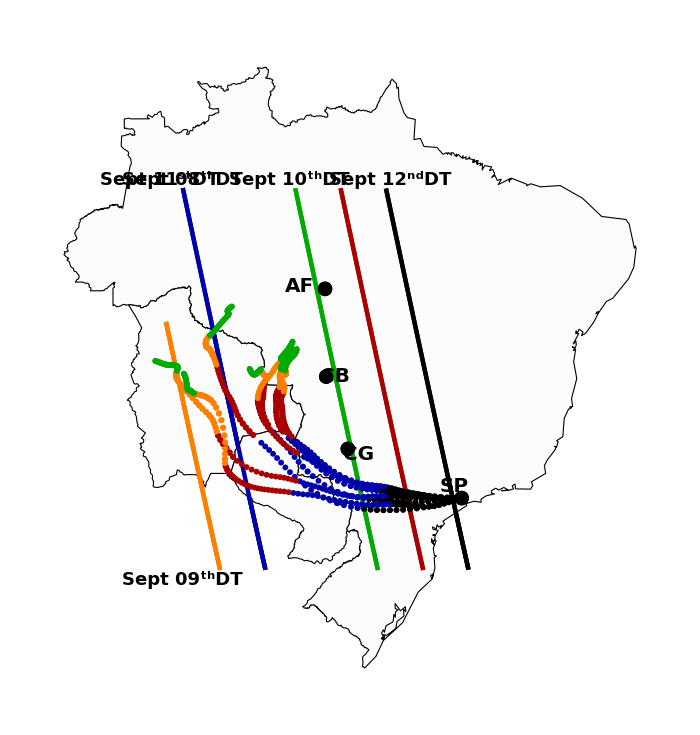

```mathematica
SDC3=Graphics[{EdgeForm[Black],RGBColor[0.99,0.99,0.99],Polygon[Map[GeoGridPosition[GeoPosition[#],"Mercator"]⟦1⟧&,CountryData[#,"Coordinates"],{2}]],Darker[Black],Thickness[.0045],PlotLabel->"Round",
Line/@Map[GeoGridPosition[GeoPosition[#],"Mercator"]⟦1⟧&,{trajectory⟦10⟧},{2}],
Darker[Blue],Thickness[.0045],PlotLabel->"Round",
Line/@Map[GeoGridPosition[GeoPosition[#],"Mercator"]⟦1⟧&,{trajectory⟦8⟧},{2}],
Darker[Red],Thickness[.0045],PlotLabel->"Round",
Line/@Map[GeoGridPosition[GeoPosition[#],"Mercator"]⟦1⟧&,{trajectory⟦6⟧},{2}],
Orange,Thickness[.0045],PlotLabel->"Round",
Line/@Map[GeoGridPosition[GeoPosition[#],"Mercator"]⟦1⟧&,{trajectory⟦4⟧},{2}],
Darker[Green],Thickness[.0045],PlotLabel->"Round",
Line/@Map[GeoGridPosition[GeoPosition[#],"Mercator"]⟦1⟧&,{trajectory⟦3⟧},{2}],
Darker[Black],PointSize[.006],Point/@Map[GeoGridPosition[GeoPosition[#],"Mercator"]⟦1⟧&,{latlonghy01},{2}],
Darker[Blue],PointSize[.006],Point/@Map[GeoGridPosition[GeoPosition[#],"Mercator"]⟦1⟧&,{latlonghy02},{2}],
Darker[Red],PointSize[.006],Point/@Map[GeoGridPosition[GeoPosition[#],"Mercator"]⟦1⟧&,{latlonghy03},{2}],
Orange,PointSize[.006],Point/@Map[GeoGridPosition[GeoPosition[#],"Mercator"]⟦1⟧&,{latlonghy04},{2}],
Darker[Green],PointSize[.006],Point/@Map[GeoGridPosition[GeoPosition[#],"Mercator"]⟦1⟧&,{latlonghy05},{2}],
Darker[Black],PointSize[.015],Point/@Map[GeoGridPosition[GeoPosition[#],"Mercator"]⟦1⟧&,{altafloresta},{2}]}&/@ SDD3,
Epilog->{Text[StyleForm["AF",FontSize->20,FontWeight->"Bold"],Scaled[{0.44,0.63}],{0.5,0}],
Text[StyleForm["CB",FontSize->20,FontWeight->"Bold"],Scaled[{0.5,0.485}],{0.5,0}],
Text[StyleForm["CG",FontSize->20,FontWeight->"Bold"],Scaled[{0.54,0.36}],{0.5,0}],
Text[StyleForm["SP",FontSize->20,FontWeight->"Bold"],Scaled[{0.7,0.31}],{0.5,0}],
Text[StyleForm["Sept 12^ndDT",FontSize->18,FontWeight->"Bold"],Scaled[{0.67,0.80}],{0.5,0}],
Text[StyleForm["Sept 11^stDT",FontSize->18,FontWeight->"Bold"],Scaled[{0.28,0.80}],{0.5,0}],
Text[StyleForm["Sept 10^thDT",FontSize->18,FontWeight->"Bold"],Scaled[{0.50,0.80}],{0.5,0}],
Text[StyleForm["Sept 09^thDT",FontSize->18,FontWeight->"Bold"],Scaled[{0.32,0.16}],{0.5,0}],
Text[StyleForm["Sept 08^thDT",FontSize->18,FontWeight->"Bold"],Scaled[{0.32,0.80}],{0.5,0}]},
ImageSize->700]
```

```mathematica
Export["2012_09_12_HYSPLIT_CALIPSO_partial_trajectories_NT.tiff",SDC3];
```

## Overpass

```mathematica
dist1=Table[Array[t,Length[trajectory⟦trajCAL⟧]],{i,1,Length[latlonghy01]}];
```

```mathematica
For[i=1,i≤Length[latlonghy01],
For[j=1,j≤ Length[trajectory⟦trajCAL⟧],
Do[ dist1⟦i⟧⟦j⟧=N[GeoDistance[latlonghy01⟦i⟧,trajectory⟦trajCAL⟧⟦j⟧]]  ];

j++];
i++];
```

```mathematica
cd=Min[Table[Min[dist1⟦i⟧],{i,1,Length[dist1]}]]/1000
```

1.70007

```mathematica
cdmin=Position[Table[Min[dist1⟦i⟧],{i,1,Length[dist1]}],Min[Table[Min[dist1⟦i⟧],{i,1,Length[dist1]}]]]
```

{{93}}

```mathematica
latlongcd=Flatten[latlonghy01⟦Flatten[cdmin]⟧,1]
```

{-24.311,-52.544}